```mathematica
E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-a Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1
E1b[n_,k_,b_]:=Sum[ Binomial[k,j] E2a[n,k-j,b],{j,0,k}]
E1b[n_,z_,b_]:=Expand[Sum[bins[z,a]E2a[n,a,b],{a,0,Log[If[ b < 2, b, 2],n]}]]
E1c[n_,z_,b_] := Expand[FullSimplify[(E1b[n,z+1,b]-1)/(z+1)]]
```

```mathematica
E1b[100,z,3/2]
```

1-(8149753 z)/2365440+(44308889 z^2)/6451200-(3885851 z^3)/1075200-(47910697 z^4)/41287680+(32326801 z^5)/13762560-(159089057 z^6)/117964800+(110725357 z^7)/275251200-(490059 z^8)/9175040+(21519 z^9)/9175040+(2673 z^10)/91750400-(2187 z^11)/1009254400

```mathematica
E1c[100,z,3/2]
```

(823345 z)/946176-(856706161 z^2)/567705600+(343389241 z^3)/324403200-(70576831 z^4)/1135411200+(706832933 z^5)/9083289600+(290809943 z^6)/3027763200-(17086851 z^7)/504627200+(1266651 z^8)/504627200+(7533 z^9)/1009254400-(2187 z^10)/1009254400

```mathematica
bins[ z_, a_] := Product[ (z-k),{k,0,a-1}]/a!
D2a[n_,k_]:=D2a[n,k]=Sum[D2a[Floor[n/j],k-1],{j,2,n}];D2a[n_,0]:=1
D1a[n_,k_]:=Sum[ bins[k,j] D2a[n,k-j],{j,0,k}]
D1a[n_,z_]:=Expand[Sum[bins[z,a]D2a[n,a],{a,0,Log[2,n]}]]
D1c[n_,z_] := Expand[FullSimplify[(D1a[n,z+1]-1)/(z+1)]]
```

```mathematica
D1a[100,x]
```

1+(428 x)/15+(16289 x^2)/360+(331 x^3)/16+(611 x^4)/144+(67 x^5)/240+(7 x^6)/720

```mathematica
D1c[100,x]
```

99+(6031 x)/60+(3167 x^2)/90+(3929 x^3)/720+(59 x^4)/180+(7 x^5)/720

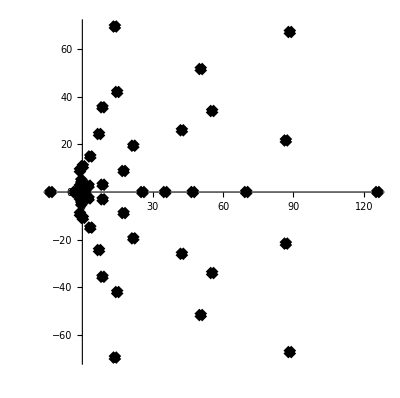

```mathematica
RootLocusPlot[1/Expand[E1c[100,x,11/10]],{k,0,1},FeedbackType->None]
```

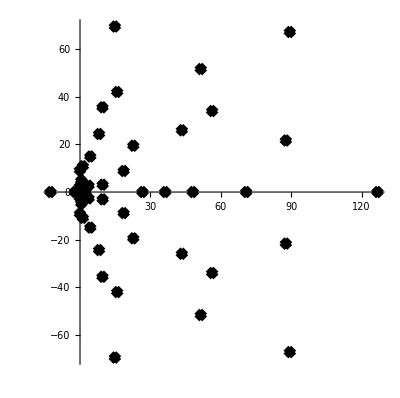

```mathematica
RootLocusPlot[1/Expand[E1b[100,x,11/10]],{k,0,1},FeedbackType->None]
```